# 1. Preparing files

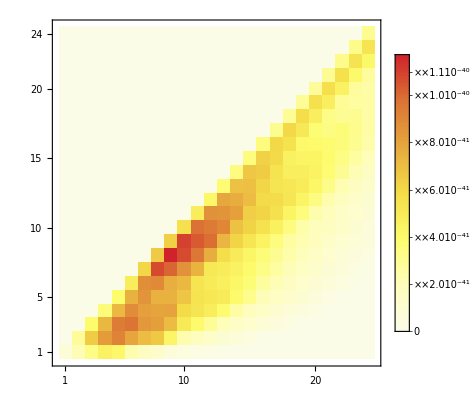

```mathematica
path="/home/michaszko/Documents/Neutrina/Opus/MINERvA_anu";
type="LFG";
scalingFactor=10^41;
mecDim=24;
eventsNumber=10^6;
crossSection=8.65493*10^-40;

Subscript[Δp, T]={150,100,150,300,300,500};
dpT={150,250,400,700,1000,1500};
dpT2=dpT-Subscript[Δp, T]/2;
Subscript[Δp, L]={500,500,500,500,500,1000,1000,2000,2000,5000};
dpL={1500,2000,2500,3000,3500,4000,5000,6000,8000,10000,15000};
widthVanilla=Flatten[KroneckerProduct[Subscript[Δp, T],Subscript[Δp, L]]];

lenPT=Length[Subscript[Δp, T]];
lenPL=Length[Subscript[Δp, L]];

(*******************************)

mecVanillaDist=Import[path<>"/data/matrix_"<>type<>".dat"];
nonmecVanillaMatrix=Import[path<>"/data/cros_total_nuwro_"<>type<>".dat"];
danielVanillaMatrix=Transpose[Import[path<>"/data/cros_total_daniel.dat"]]/scalingFactor;
covNonVanilla=Import[path<>"/data/daniel_covariance_vanilla.dat"]/scalingFactor^2;
covVanilla=PseudoInverse[covNonVanilla];
errorVanillaMatrix=1/Transpose[Sqrt[Partition[Diagonal[covVanilla],10]]];

(*****************************************)

mecDist=mecVanillaDist/eventsNumber*crossSection*1000000/widthVanilla*12/13;
errorVanillaMatrixError = errorVanillaMatrix/.(y_/;y==0)->1;

(**********************************************)

MatrixPlot[Transpose@mecDist];

RectangleChart[
Thread[{Subscript[Δp, T],Take[Plus@@Transpose[mecDist],{#,-1,lenPL}]}],
GridLines->Automatic,
BarSpacing->None,
ImageSize->Large,
PlotLabel->(#-1)]&/@Range[lenPL-1];

MatrixPlot[Partition[Plus@@mecDist,mecDim],DataReversed->True,PlotLegends->Automatic, ColorFunction->"TemperatureMap"]
```

# 2. Test χ^2

## χ^2 w/o covariance

```mathematica
newVanillaMatrix=Transpose@Partition[mecDist.ConstantArray[1,mecDim^2],lenPL];


x=((danielVanillaMatrix-nonmecVanillaMatrix-newVanillaMatrix)/errorVanillaMatrixError)^2;

χ=Total[x,2]
```

135.139

## χ^2 with covariance

```mathematica
newVanillaMatrix=Transpose@Partition[mecDist.ConstantArray[1,mecDim^2],lenPL];
a=Flatten[Transpose[danielVanillaMatrix-nonmecVanillaMatrix-newVanillaMatrix]];
a.covVanilla.a
```

105.658

# 3. Solution

```mathematica
emptyValue=1;

V=Table[Subscript[v, i,j],{i,1,mecDim},{j,1,mecDim}] ;
V1=Flatten@Table[Subscript[v, i,j],{i,1,mecDim},{j,i,mecDim}];
V2=Flatten@Table[Subscript[v, i,j],{i,2,mecDim},{j,1,i-1}];
V3=Flatten[V/.Thread[V2->emptyValue]];

chi2[x_]:=Total[
((danielVanillaMatrix-nonmecVanillaMatrix-Transpose@Partition[mecDist.x,lenPL])/errorVanillaMatrixError)^2,2]

chi2cov[x_]:=(Flatten[Transpose[danielVanillaMatrix-nonmecVanillaMatrix-Transpose@Partition[mecDist.x,lenPL]]]).covVanilla.(Flatten[Transpose[danielVanillaMatrix-nonmecVanillaMatrix-Transpose@Partition[mecDist.x,lenPL]]])

plotMec[x_,fun_]:=MatrixPlot[
Partition[x,mecDim],
PlotLegends->Automatic,
DataReversed->True,
PlotLabel->{"χ_cov^2 = "<> ToString[chi2cov[x]]<>" ,χ_non^2 = " <> ToString[chi2[x]]}]


(*condition[p_]=Module[{a},
a=Join[
Thread[V1≥ 0],
Flatten[Table[Abs[Subscript[v, i,j]-Subscript[v, i,j+1]]/(Subscript[v, i,j]+Subscript[v, i,j+1])<p,{i,1,mecDim},{j,i,mecDim-1}]],
Flatten[Table[Abs[Subscript[v, i,j]-Subscript[v, i+1,j]]/(Subscript[v, i,j]+Subscript[v, i+1,j])<p,{j,1,mecDim},{i,1,j-1}]]];
And@@a];*)

condition[p_]=Module[{a},
a=Join[
Thread[V1≥ 0],
 (*inner elements*)
Flatten[Table[Subscript[v, i,j]/Min[{Subscript[v, i,j+1],Subscript[v, i,j-1],Subscript[v, i+1,j],Subscript[v, i-1,j]}]<1/(1-p),
{i,2,mecDim-1},{j,i+1,mecDim-1}]],

Flatten[Table[Subscript[v, i,j]/Max[{Subscript[v, i,j+1],Subscript[v, i,j-1],Subscript[v, i+1,j],Subscript[v, i-1,j]}]>(1-p),
{i,2,mecDim-1},{j,i+1,mecDim-1}]],

(*diagonal elements*)
Flatten[Table[Subscript[v, i,j]/Min[{Subscript[v, i,j+1],Subscript[v, i-1,j]}]<1/(1-p),
{i,2,mecDim-1},{j,i,i}]],

Flatten[Table[Subscript[v, i,j]/Max[{Subscript[v, i,j+1],Subscript[v, i-1,j]}]>(1-p),
{i,2,mecDim-1},{j,i,i}]],
(*top(bottom) row*)

Flatten[Table[Subscript[v, 1,j]/Min[{Subscript[v, 1,j+1],Subscript[v, 1,j-1],Subscript[v, 1+1,j]}]<1/(1-p),
{j,2,mecDim-1}]],

Flatten[Table[Subscript[v, 1,j]/Max[{Subscript[v, 1,j+1],Subscript[v, 1,j-1],Subscript[v, 1+1,j]}]>1-p,
{j,2,mecDim-1}]],

(*right side*)

Flatten[Table[Subscript[v, i,mecDim]/Min[{Subscript[v, i,mecDim-1],Subscript[v, i-1,mecDim],Subscript[v, i+1,mecDim]}]<1/(1-p),
{i,2,mecDim-1}]],


Flatten[Table[Subscript[v, i,mecDim]/Max[{Subscript[v, i,mecDim-1],Subscript[v, i-1,mecDim],Subscript[v, i+1,mecDim]}]>1-p,
{i,2,mecDim-1}]],

{Subscript[v, 1,1]/Subscript[v, 1,2]>1-p,Subscript[v, 1,1]/Subscript[v, 1,2]<1/(1-p),Subscript[v, 24,24]/Subscript[v, 23,24]>1-p,Subscript[v, 24,24]/Subscript[v, 23,24]<1/(1-p)}];

And@@a];

minChi2[fun_,p_,iter_:100,init_:Automatic,print_:False]:=Module[{a,b,c,meth},
meth="InteriorPoint";
{a,b}=NMinimize[
{fun[V3],condition[p]},
V1,
MaxIterations->iter,
Method->{"RandomSearch","SearchPoints"->1,"RandomSeed"-> RandomInteger[1000],Method->meth,"InitialPoints"->init},

StepMonitor:>(
Export[path<>"/results/chi2Values/"<>ToString[fun]<>"_"<>ToString[fun[V3]]<>"_maxIter_"<>ToString[iter]<>"_continuous_"<>ToString[p]<>"_"<>meth<>".dat",Partition[V3,mecDim]];

If[print==True,Print[plotMec[V3,fun]]])
];

Export[path<>"/results/chi2ValuesFinal/"<>ToString[fun]<>"_"<>ToString[fun[V3/.b]]<>"_maxIter_"<>ToString[iter]<>"_continuous_"<>ToString[p]<>"_"<>meth<>".dat",Partition[V3/.b,mecDim]];

(*c=chi2[V3/.b];*)
c="not available";
{a,c}
]
```

## χ^2

```mathematica
low=Import [path<>"/results/chi2ValuesFinal/chi2cov_79.6237_maxIter_10_continuous_0.4_InteriorPoint.dat"];
low=Flatten[low/. 1->Nothing];
minChi2[chi2cov,0.4,100,{low}]
(*minChi2[chi2cov,0.4,10]*)
```

{72.5519,not available}

# 4. Plots of results

```mathematica
Needs["ErrorBarPlots`"]
tmp=Import ["/home/michaszko/Documents/Neutrina/Opus/MINERvA_nu/results/chi2ValuesFinal/tomek_final.dat"];

q=Flatten[Transpose@nonmecVanillaMatrix];
w=Flatten[Partition[mecDist.Flatten[ConstantArray[1,24^2]],lenPL]];
v=Flatten[Partition[mecDist.Flatten[tmp],lenPL]];

aa=Flatten[Transpose@nonmecVanillaMatrix+Partition[mecDist.Flatten[ConstantArray[1,24^2]],lenPL]];
bb=
Flatten[Transpose@nonmecVanillaMatrix+Partition[mecDist.Flatten[tmp],lenPL]];
cc=
Flatten[Transpose@danielVanillaMatrix];

lol1=Flatten[Thread[{dpT2,Take[cc,{#,-1,lenPL}]}]&/@Range[lenPL],1];
lol2=ErrorBar[#]&/@Flatten[errorVanillaMatrix];
dd=Partition[Thread[{lol1,lol2}],lenPT];

a=RectangleChart[
Thread[{Thread[{Subscript[Δp, T],Take[q,{#,-1,lenPL}]}],Thread[{Subscript[Δp, T],Take[w,{#,-1,lenPL}]}]}],
GridLines->Automatic,
BarSpacing->None,
ImageSize->Full,
ChartStyle->{Red,Yellow},
PlotLabel->Text[Style["CC 0π (ν̄)_μ, MINERvA_anu, NuWro before rescaling, " <> ToString[dpL[[#]]]<>" < p_L < "<>ToString[dpL[[#+1]]] <> " [MeV]"(*",\n χ_cov^2 = " <> ToString[chi2cov[ConstantArray[1,mecDim^2]]]<>" , χ_noncov^2 = " <> ToString[chi2[Flatten[tmp]]] *),FontSize->17]],
FrameLabel->{Text[Style["p_T [MeV]",FontSize->17]],Text[Style["cross section (per nucleon) [cm^2/GeV^2/nucleon]",FontSize->17]]},
Frame->True,
Axes->False,
Background->White,
ChartLayout->"Stacked",
ChartStyle->EdgeForm[None],
ColorFunction->(EdgeForm[None]&),
PlotRange->{{0,Last[dpT]},Automatic},
ChartLegends->Placed[{Text[Style["non-MEC",Large]],Text[Style["MEC",Large]]},{Right,Top}],
PlotLabel->(#-1)]&/@Range[lenPL];

b=RectangleChart[
Thread[{Thread[{Subscript[Δp, T],Take[q,{#,-1,lenPL}]}],Thread[{Subscript[Δp, T],Take[v,{#,-1,lenPL}]}]}],
GridLines->Automatic,
BarSpacing->None,
ImageSize->Full,
ChartStyle->{Red,Yellow},
PlotLabel->Text[Style["CC 0π (ν̄)_μ, MINERvA_nu, NuWro after rescaling, " <> ToString[dpL[[#]]]<>" < p_L < "<>ToString[dpL[[#+1]]] <> " [MeV]"(*",\n χ_cov^2 = " <> ToString[chi2cov[Flatten[tmp]]]<>" , χ_noncov^2 = " <> ToString[chi2[Flatten[tmp]]]*),FontSize->17]],
FrameLabel->{Text[Style["p_T [MeV]",FontSize->17]],Text[Style["cross section (per nucleon) [cm^2/GeV^2/nucleon]",FontSize->17]]},
Frame->True,
Axes->False,
Background->White,
ChartLayout->"Stacked",
ChartStyle->EdgeForm[None],
ColorFunction->(EdgeForm[None]&),
PlotRange->{{0,Last[dpT]},Automatic},
ChartLegends->Placed[{Text[Style["non-MEC",Large]],Text[Style["MEC",Large]]},{Right,Top}],
PlotLabel->(#-1)]&/@Range[lenPL];

c=ListStepPlot[
Thread[{Join[dpT-Subscript[Δp, T],{Last[dpT]}],Join[Take[cc,{#,-1,lenPL}],{0}]}],
Right,
GridLines->Automatic,
Joined->False,
ImageSize->Full,
PlotStyle->{Black,Thickness[0.004]},
PlotRange->{0,Last[dpT]},
PlotLabel->(#-1)]&/@Range[lenPL];


d=ErrorListPlot[
dd[[#]],
GridLines->Automatic,
ImageSize->Full,
DataRange->{0,Last[dpT]},
PlotStyle->{Black,Thickness[0.002],PointSize[0]},
PlotLabel->(#-1)]&/@Range[lenPL];

(*Show[{a[[#]],c[[#]],d[[#]]}]&[2]*)

Export[path<>"/plots/histogramsBefore/"<>ToString[#]<>".pdf",Show[a[[#]],c[[#]],d[[#]]]]&/@Range[lenPL];
Export[path<>"/plots/histogramsAfter/"<>ToString[#]<>".pdf",Show[b[[#]],c[[#]],d[[#]]]]&/@Range[lenPL];
(*Export[path<>"/plots/histogramsTogether/"<>ToString[#]<>".pdf",Show[{b[[#]],a[[#]],c[[#]],d[[#]]}]]&/@Range[lenPL];*)
```

# 5. Tests

```mathematica
tmp2=Import [path<>"/results/chi2Values/chi2cov_342.223_maxIter_100_continuous_0.4_InteriorPoint.dat"];
tmp3=Flatten[tmp2/. 1->Nothing];
var=Thread[V1->tmp3];
p=0.4;

Join[
Flatten[Table[Subscript[v, i,j]/Min[{Subscript[v, i,j+1],Subscript[v, i,j-1],Subscript[v, i+1,j],Subscript[v, i-1,j]}],
{i,2,mecDim-1},{j,i+1,mecDim-1}]],


Flatten[Table[Subscript[v, i,j]/Min[{Subscript[v, i,j+1],Subscript[v, i-1,j]}],
{i,2,mecDim-1},{j,i,i}]],


Flatten[Table[Subscript[v, 1,j]/Min[{Subscript[v, 1,j+1],Subscript[v, 1,j-1],Subscript[v, 1+1,j]}],
{j,2,mecDim-1}]],


Flatten[Table[Subscript[v, i,mecDim]/Min[{Subscript[v, i,mecDim-1],Subscript[v, i-1,mecDim],Subscript[v, i+1,mecDim]}],
{i,2,mecDim-1}]],


{Subscript[v, 1,1]/Subscript[v, 1,2],Subscript[v, 24,24]/Subscript[v, 23,24]}]/.var;

ListPlot[
{%,ConstantArray[1/(1-p),300],ConstantArray[1-p,300]},
PlotLabel->"(v_(i, j))/Min[{SubscriptBox[v, i, j + 1], SubscriptBox[v, i, j - 1], SubscriptBox[v, i + 1, j], SubscriptBox[v, i - 1, j]}]<1/(1 - p);  χ^2=320.087",
Frame->True,
FrameLabel->{,α},
PlotRange->{0,5}]

Count[Thread[%%<=1/(1-0.4)+0.000001],False]



Join[
Flatten[Table[Subscript[v, i,j]/Max[{Subscript[v, i,j+1],Subscript[v, i,j-1],Subscript[v, i+1,j],Subscript[v, i-1,j]}],
{i,2,mecDim-1},{j,i+1,mecDim-1}]],


Flatten[Table[Subscript[v, i,j]/Max[{Subscript[v, i,j+1],Subscript[v, i-1,j]}],
{i,2,mecDim-1},{j,i,i}]],


Flatten[Table[Subscript[v, 1,j]/Max[{Subscript[v, 1,j+1],Subscript[v, 1,j-1],Subscript[v, 1+1,j]}],
{j,2,mecDim-1}]],


Flatten[Table[Subscript[v, i,mecDim]/Max[{Subscript[v, i,mecDim-1],Subscript[v, i-1,mecDim],Subscript[v, i+1,mecDim]}],
{i,2,mecDim-1}]],


{Subscript[v, 24,24]/Subscript[v, 23,24],Subscript[v, 1,1]/Subscript[v, 1,2]}
]/.var;

ListPlot[
{%,ConstantArray[1-p,300],ConstantArray[1/(1-p),300]},
PlotLabel->"(v_(i, j))/Max[{SubscriptBox[v, i, j + 1], SubscriptBox[v, i, j - 1], SubscriptBox[v, i + 1, j], SubscriptBox[v, i - 1, j]}]>1-p;  χ^2=320.087",
Frame->True,
FrameLabel->{,α},
PlotRange->{0,5}
]

Count[Thread[%%>0.6-0.000001],False]
```

```mathematica
tmp2=Import [path<>"/results/chi2ValuesFinal/tomek.dat"];
chi2cov[Flatten@tmp2]
```

76.3171